### Tanh fit

Use this to find the sigmoidal CURVE, such as Tatsuya found when stress granules were being formed after As stress. 
THEN, you can use this to shift other data and align your cells on the instance of a cell process... 
Such as, when stress granules are at 10% (myBlue10per)

MAYBE! Use this for my cy3 accumulation data??

```mathematica
myBlueNumber=Length/@myBlueSpots;
```

```mathematica
fitUpto=15;
```

```mathematica
nlm=NonlinearModelFit[myBlueNumber⟦;;fitUpto⟧,a*(1+Tanh[b*x-c])/2,{a,b,c},x];
```

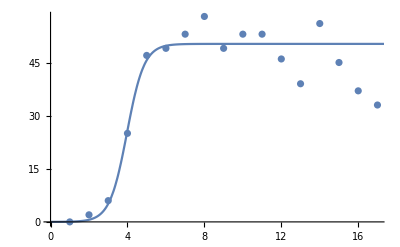

```mathematica
Show[ListPlot@myBlueNumber,Plot[nlm@x,{x,0,20}]]
```

```mathematica
myBlue10per=Solve[nlm@x==0.1*nlm["BestFitParameters"]⟦1,2⟧,x]⟦1,1,2⟧
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

2.99049

```mathematica
nlm>>(analysisFolder<>"_blueFit.dat");
myBlue10per>>(analysisFolder<>"_blue10per.dat");
```